## Problem:

The following video showed up in my YouTube recommendations and it seemed like a very interesting problem to solve numerically in  Mathematica. So I figured I’d share it with all of you and type up the solution, because it’s very “easy” to do in Mathematica in the sense that it only really takes about 6 lines. However it requires a pretty good mastery of Mathematica functions and patterns like we talked about in the first few weeks of class. And also requires you to be a bit clever. As such, I recommend taking a stab at it yourself! Anyway, here is the video https://www.youtube.com/watch?v=iBxVRwynmmE

And here is the problem statement from the video:
-Graphics-

## Hint

First we need to re-arrange the equalities so they’re all an expression of f[n] we will do this by substituting in u=2n and solving for f[u] for the first two examples, and then letting u = 2n+1 and solving for f[u] in the bottom two examples. While also seeing what this does to the conditions:

For u = 2n   ⇒  n = u/2
	Eq 1.		f[u] = f[u/2] when u/2 is even and u is an integer
	Eq 2. 	f[u] = 2 f[u/2] when u/2is odd and u is an integer
For u = 2n+1  ⇒ n = (u-1)/2 
	Eq 3. 	f[u] = 2 f[(u-1)/2]+1 when (u-1)/2 is even and u is an integer
	Eq 4. 	f[u] = f[(u-1)/2] when (u-1)/2 is odd and u is an integer

## Big Spoiler (Most of the solution)

Now that we have these relationships, we can set up a function in Mathematica which uses these evaluation rules

```mathematica
ClearAll[f]
f[1]=1;
f[u_?IntegerQ/;EvenQ[u/2]]:=f[u]=f[u/2];
f[u_?IntegerQ/;OddQ[u/2]]:=f[u]=2f[u/2];
f[u_?IntegerQ/;EvenQ[(u-1)/2]]:=f[u]=2f[(u-1)/2]+1;
f[u_?IntegerQ/;OddQ[(u-1)/2]]:=f[u]=f[(u-1)/2];
```

## Last bit of the solution, and final answer

Now that we have a function we can plug any number into,  we make a list of all the numbers between 0 and 2011 and use Cases to grab the numbers where f[n]=f[2011] is true. Then we use length to count them by measuring the length of the resulting list. We also use Framed to box our final answer!

```mathematica
Cases[Table[n,{n,1,2010}],n_/;f[n]==f[2011]]//Length//Framed
```

455

So we can see there are 455 numbers less than 2011 where f[n] is the same as f[2011]. Additionally, we can also print all these numbers in the same way

```mathematica
Cases[Table[n,{n,1,2010}],n_/;f[n]==f[2011]]
```

{21,37,41,43,45,53,69,73,75,77,81,83,87,89,91,93,101,105,107,109,117,133,137,139,141,145,147,151,153,155,157,161,163,167,175,177,179,183,185,187,189,197,201,203,205,209,211,215,217,219,221,229,233,235,237,245,261,265,267,269,273,275,279,281,283,285,289,291,295,303,305,307,311,313,315,317,321,323,327,335,351,353,355,359,367,369,371,375,377,379,381,389,393,395,397,401,403,407,409,411,413,417,419,423,431,433,435,439,441,443,445,453,457,459,461,465,467,471,473,475,477,485,489,491,493,501,517,521,523,525,529,531,535,537,539,541,545,547,551,559,561,563,567,569,571,573,577,579,583,591,607,609,611,615,623,625,627,631,633,635,637,641,643,647,655,671,703,705,707,711,719,735,737,739,743,751,753,755,759,761,763,765,773,777,779,781,785,787,791,793,795,797,801,803,807,815,817,819,823,825,827,829,833,835,839,847,863,865,867,871,879,881,883,887,889,891,893,901,905,907,909,913,915,919,921,923,925,929,931,935,943,945,947,951,953,955,957,965,969,971,973,977,979,983,985,987,989,997,1001,1003,1005,1013,1029,1033,1035,1037,1041,1043,1047,1049,1051,1053,1057,1059,1063,1071,1073,1075,1079,1081,1083,1085,1089,1091,1095,1103,1119,1121,1123,1127,1135,1137,1139,1143,1145,1147,1149,1153,1155,1159,1167,1183,1215,1217,1219,1223,1231,1247,1249,1251,1255,1263,1265,1267,1271,1273,1275,1277,1281,1283,1287,1295,1311,1343,1407,1409,1411,1415,1423,1439,1471,1473,1475,1479,1487,1503,1505,1507,1511,1519,1521,1523,1527,1529,1531,1533,1541,1545,1547,1549,1553,1555,1559,1561,1563,1565,1569,1571,1575,1583,1585,1587,1591,1593,1595,1597,1601,1603,1607,1615,1631,1633,1635,1639,1647,1649,1651,1655,1657,1659,1661,1665,1667,1671,1679,1695,1727,1729,1731,1735,1743,1759,1761,1763,1767,1775,1777,1779,1783,1785,1787,1789,1797,1801,1803,1805,1809,1811,1815,1817,1819,1821,1825,1827,1831,1839,1841,1843,1847,1849,1851,1853,1857,1859,1863,1871,1887,1889,1891,1895,1903,1905,1907,1911,1913,1915,1917,1925,1929,1931,1933,1937,1939,1943,1945,1947,1949,1953,1955,1959,1967,1969,1971,1975,1977,1979,1981,1989,1993,1995,1997,2001,2003,2007,2009}

## Some other stuff for fun

Lets go ahead and plot the function from n=0 to n=2011 to see what it looks like and also show a horizontal line to see all the points we’re trying to find

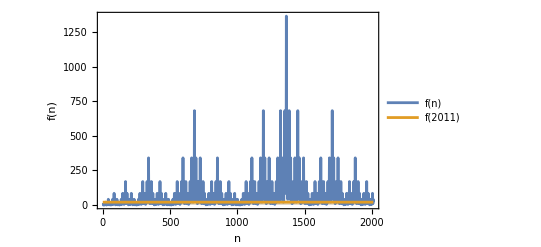

```mathematica
DiscretePlot[{f[n],f[2011]},{n,2011},PlotRange->All,PlotLegends->{"f(n)","f(2011)"},Frame->True,FrameLabel->{"n","f(n)"}]
```